```mathematica
circles:=ContourPlot[Evaluate[Flatten[Table[(x-n)^2+(y-m)^2==ρ^2,{n,-3,3},{m,-3,3}]]],{x,-3,3},{y,-3,3},Axes->True,AspectRatio->Automatic,ContourStyle->Black]
```

```mathematica
ρ:=0.3
```

```mathematica
(* Points obtained by classical algorithm *)
```

```mathematica
points:={{0.4,0.1},{0.22924952910108745,0.19350621025416642},{0.05283194463606211,0.7046886632281584},{0.06177169928112605,0.2935715537444358},{0.768731955664866,1.8089107756324223},{-1.7549257396828621,1.1730277634658894},{-1.278253524817416,1.887861799877635},{-1.700617935559081,1.9807547540651356},{-1.299563417407707,2.0161789663148117},{-1.7168158123204487,2.0990288637129226},{-1.1661377215190767,2.7502035679028825}}
```

```mathematica
(* println(collisions([0.5,0.1],[-0.42,0.23],0.3,10)[1]) *)
```

```mathematica
Show[circles,ListPlot[points,Joined->True,PlotStyle->Directive[Thickness[0.005]]]]
```

```mathematica
{{0.0,0.35},{0.9641445552106563,0.9066491184885844},{1.901566855409655,-1.982367188367812},{1.0999748803884173,-2.9977587299757396},{1.9177056142378983,-3.9431877295644826},{-5.930360381365476,-1.07176575448247},{-4.990843003801113,-3.900420135465981},{-3.997705464350009,-2.099973672064954}}
```

```mathematica
ρ:=0.1
```

```mathematica
points:={{0.0,0.35},{0.9641445552106563,0.9066491184885844},{1.901566855409655,-1.982367188367812},{1.0999748803884173,-2.9977587299757396},{1.9177056142378983,-3.9431877295644826},{-5.930360381365476,-1.07176575448247},{-4.990843003801113,-3.900420135465981},{-3.997705464350009,-2.099973672064954}}
```

```mathematica
(* Trajectory starting from (0, 0.35) *)
```

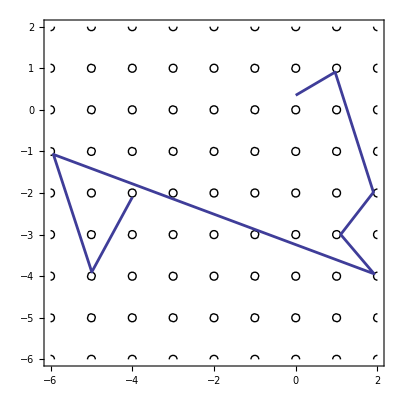

```mathematica
Show[circles,ListPlot[points,Joined->True,PlotStyle->Directive[Thickness[0.005]]]]
```

```mathematica
points:={{0,0.445},{0.94488,1.91656}}
```

```mathematica
(* Initial conditions x = (0, 0.445), v = (cos 1, sin 1), ρ = 0.1 *)
```

```mathematica
points:={{0.0,0.445},{0.94488,1.91656},{-0.971676,-0.904095},{-0.989769,-0.0994753},{-0.0924276,-4.96183},{-2.93286,-6.92589},{0.901081,-0.0146626}}
```

```mathematica
(* Classical trajectory for these initial conditions *)
```

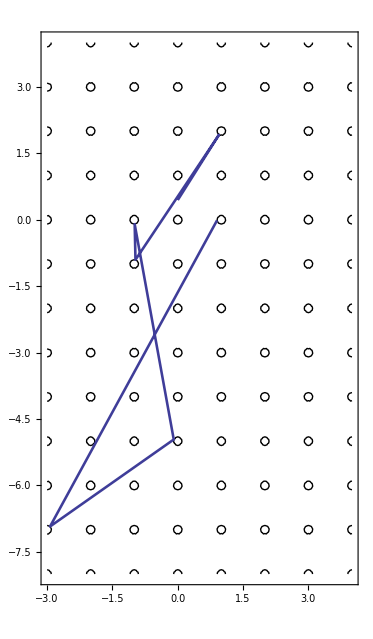

```mathematica
Show[circles,ListPlot[points,Joined->True,PlotStyle->Directive[Thickness[0.005]]]]
```

```mathematica
(* The same but with a smaller radius of obstacles ρ = 0.05 *)
```

```mathematica
points2:={{0.0,0.445},{0.971899,1.95864},{-3.99055,-4.9509},{-4.96076,-1.03099},{-4.03126,-1.03902}}
```

```mathematica
ρ:=0.05
```

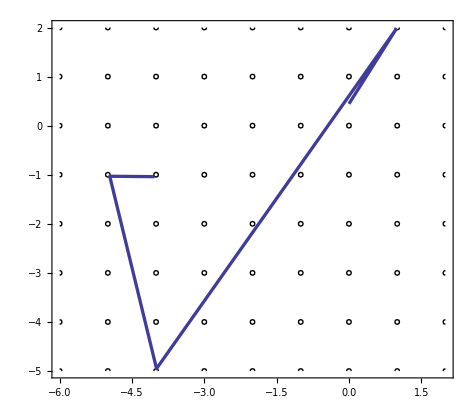

```mathematica
Show[circles,ListPlot[points2,Joined->True,PlotStyle->Directive[Thickness[0.005]]]]
```

```mathematica
(* x=0; y=0.445; vx=cos(1); vy=sin(1); r=0.1 - same classical but enlarged plot *)
```

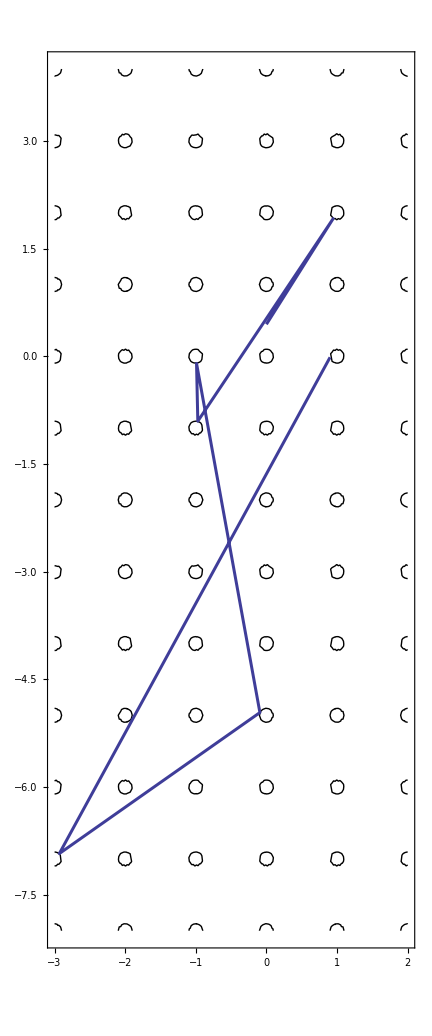

```mathematica
Show[circles,ListPlot[points,Joined->True,PlotStyle->Directive[Thickness[0.005]]]]
```

```mathematica
(*********************************************************************************)
```

```mathematica
(* Trying to find the error in first_collision() of EfficientLorentz *)
```

```mathematica
x0 := {0,0.8523674178538906}
```

```mathematica
v0 := {-0.5687431776454224,-0.8225151657457678}
```

```mathematica
k := v0[[2]]/v0[[1]]
```

```mathematica
b:=x0[[2]]-k x0[[1]]
```

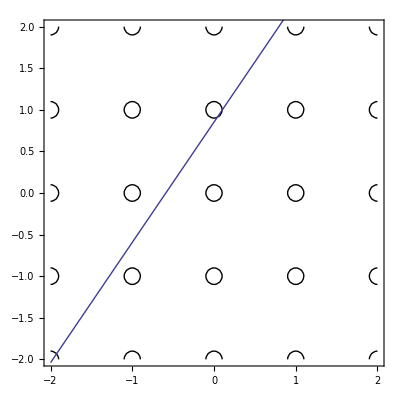

```mathematica
Show[circles,Plot[k x+b,{x,-2,2}]]
```

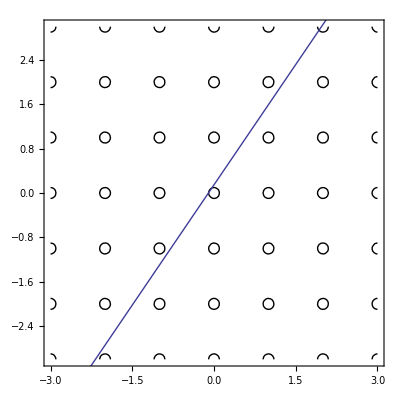

```mathematica
Show[circles,Plot[k x+1-b,{x,-3,3}]]
```

```mathematica
x0:={0,0.12}
```

```mathematica
v0={0.8,12}/Norm[{0.8,12}]
```

{0.066519,0.997785}

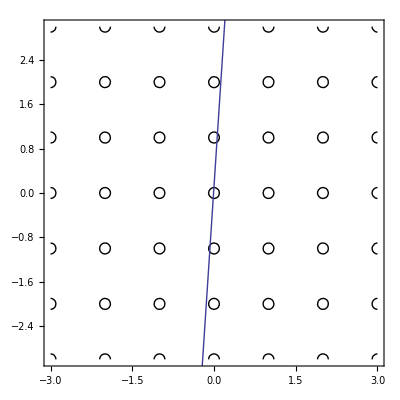

```mathematica
Show[circles,Plot[k x+b,{x,-2,2}]]
```

```mathematica
y1[x1_]:=1.2 x1+0.13
```

```mathematica
(* This formula was wrong! I found an error and fixed it. *)
```

```mathematica
dist[x_,y_,k_,b_]:=(y - k x - b)/(√(k^2+b^2))
```

```mathematica
dist[1,1,0.86,0.13]
```

0.0114973

```mathematica
dist[0,1,12,0.13]
```

0.0724957

```mathematica
dist[-1,1,-1.1,0.13]
```

-0.207646

```mathematica
dist[-1, 1, -0.9, 0.13]
```

-0.0329909

```mathematica
ϕ[b_]:=ArcTan[1-b]
```

```mathematica
l[b_]:=√(1+(1-b)^2)
```

```mathematica
dϕ[r_,b_]:=ArcSin[r/l[b]]
```

```mathematica
ψ[r_,b_]:=ArcSin[r/(1-b)]
```

```mathematica
TrigExpand[Tan[ϕ[b]-dϕ[r,b]]]
```

```mathematica
FullSimplify[-r/((1+(1-b)^2) (r/(1+(1-b)^2)-(b r)/(1+(1-b)^2)+(√(1-r^2/(1+(1-b)^2)))/(√(1+(1-b)^2))))+(√(1-r^2/(1+(1-b)^2)))/(√(1+(1-b)^2) (r/(1+(1-b)^2)-(b r)/(1+(1-b)^2)+(√(1-r^2/(1+(1-b)^2)))/(√(1+(1-b)^2))))-(b √(1-r^2/(1+(1-b)^2)))/(√(1+(1-b)^2) (r/(1+(1-b)^2)-(b r)/(1+(1-b)^2)+(√(1-r^2/(1+(1-b)^2)))/(√(1+(1-b)^2))))]
```

```mathematica
FullSimplify[(-1+b+√(2+(-2+b) b) r √(1-r^2/(2+(-2+b) b)))/(-1+r^2),b>0&&b<1&&r>0]
```

(-1+b+r √(2+(-2+b) b-r^2))/(-1+r^2)

```mathematica
TrigExpand[Tan[ϕ[b]+dϕ[r,b]]]
```

```mathematica
FullSimplify[r/((1+(1-b)^2) (-r/(1+(1-b)^2)+(b r)/(1+(1-b)^2)+(√(1-r^2/(1+(1-b)^2)))/(√(1+(1-b)^2))))+(√(1-r^2/(1+(1-b)^2)))/(√(1+(1-b)^2) (-r/(1+(1-b)^2)+(b r)/(1+(1-b)^2)+(√(1-r^2/(1+(1-b)^2)))/(√(1+(1-b)^2))))-(b √(1-r^2/(1+(1-b)^2)))/(√(1+(1-b)^2) (-r/(1+(1-b)^2)+(b r)/(1+(1-b)^2)+(√(1-r^2/(1+(1-b)^2)))/(√(1+(1-b)^2)))),b>0&&b<1&&r>0]
```

(r-(-1+b) √(2+(-2+b) b-r^2))/((-1+b) r+√(2+(-2+b) b-r^2))

```mathematica
TrigExpand[Tan[π/2-ψ[r,b]]]
```

```mathematica
FullSimplify[(√(1-r^2/(1-b)^2))/r-(b √(1-r^2/(1-b)^2))/r,b>0&&b<1&&r>0]
```

(√((-1+b)^2-r^2))/r

```mathematica
(******************************)
```

```mathematica
(* Another test: classical: collisions([0, 0.3], [cos(1.2), sin(1.2)], 0.1, 40) *)
```

```mathematica
circles:=ContourPlot[Evaluate[Flatten[Table[(x-n)^2+(y-m)^2==ρ^2,{n,-3,25},{m,0,3}]]],{x,-3,25},{y,0,3},Axes->True,AspectRatio->Automatic,ContourStyle->Black]
```

```mathematica
points:={{0.0,0.3},{1.0110656406928884,2.900614127784398},{2.9219146792616817,0.062471454962998996},{-1.9157883662346256,1.946070409434463},{-1.0335723144172106,1.094196070537321},{-0.9350814498167989,1.923936987687108},{19.969454049802543,1.0952205068592602},{21.005610680123482,1.9001575227242835},{23.964414084951475,0.093453960056057}}
```

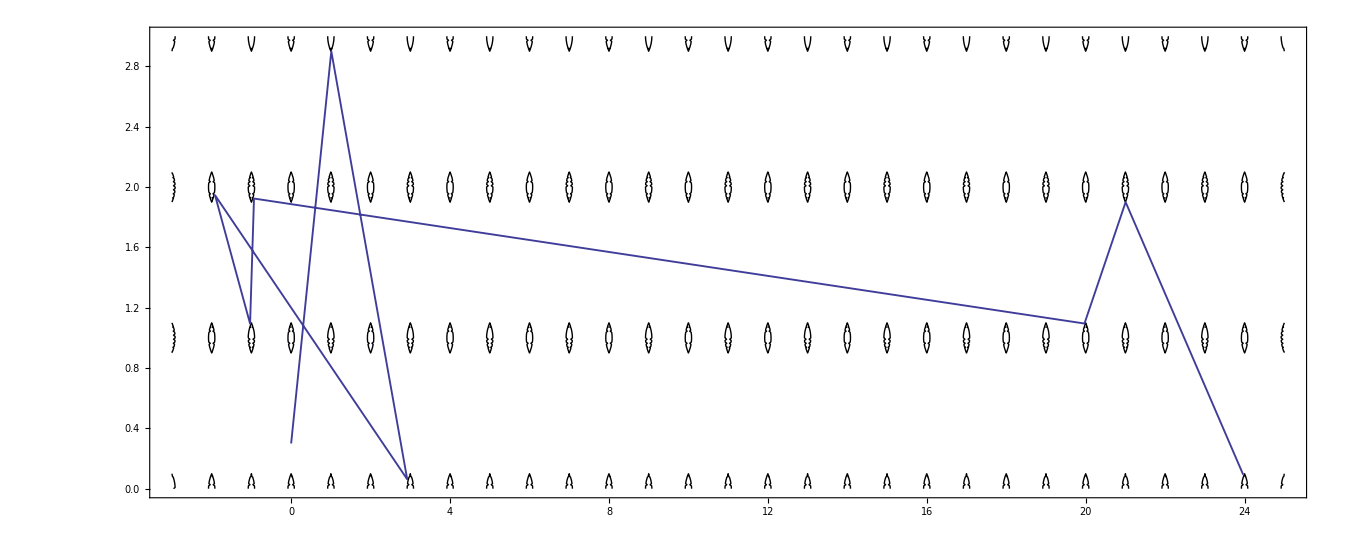

```mathematica
Show[circles,ListPlot[points,Joined->True,PlotStyle->Directive[Thickness[0.001]]]]
```

```mathematica
(* Finding out why and how the algorithm diverges *)
```

```mathematica
x0:={-25.9220385027411,24.062625912729082}
```

```mathematica
v0:={0.967026401228994,-0.2546761459699459}
```

```mathematica
k:=v0⟦2⟧/v0⟦1⟧
```

```mathematica
b:=x0⟦2⟧-k x0⟦1⟧
```

```mathematica
(* Stuff happens in the (-26, 25) neighborhood *)
```

```mathematica
circles:=ContourPlot[Evaluate[Flatten[Table[(x-n)^2+(y-m)^2==ρ^2,{n,-27,-23},{m,23,26}]]],{x,-27,-23},{y,23,26},Axes->True,AspectRatio->Automatic,ContourStyle->Black]
```

```mathematica
points:={{-23.91094892340575,24.045496216957076},{-24.035703610028186,24.906590941387062},{-24.999698062403922,24.099999544167403},{-25.956133158899803,24.91013510000067},{-25.9220385027411,24.062625912729082}}
```

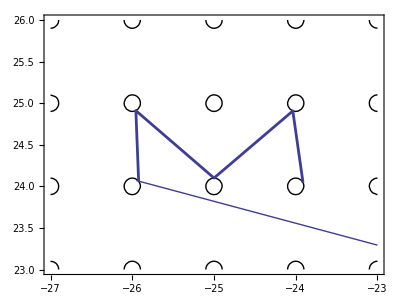

```mathematica
Show[circles,ListPlot[points,Joined->True,PlotStyle->Directive[Thickness[0.005]]],Plot[k x+b,{x,-25.95,-23}]]
```

```mathematica
dist[-26,24,k,b]
```

-0.00482416

```mathematica
dist[-25,24,k,b]
```

0.0104539

```mathematica
(* How is this possible?! The distance is clearly greater than 0.1! *)
```

```mathematica
line[x_]:=k x+b
```

```mathematica
line[-25]
```

23.8198

```mathematica
24-k*(-25)-b
```

0.180202

```mathematica
√(k^2+b^2)
```

17.2378

```mathematica
line[-25]-24
```

-0.180202

```mathematica
(* Error found in formula p. 69 UNAM notebook 1 *)
```

```mathematica
ρ:=0.1
```

```mathematica
circles:=ContourPlot[Evaluate[Flatten[Table[(x-n)^2+(y-m)^2==ρ^2,{n,-27,2},{m,-8,27}]]],{x,-27,2},{y,-8,27},Axes->True,AspectRatio->Automatic,ContourStyle->Black,PlotRange->{{-27,2},{-8,27}}]
```

```mathematica
points:={{0.0,0.445},{0.9448796725624946,1.9165629009182235},{-0.9716764156856601,-0.9040949710829063},{-0.9897690501214653,-0.0994752615708192},{-0.09242759468202599,-4.9618275001958825},{-2.9328562249389405,-6.925893903958246},{0.9010807499311531,-0.014662263325179836},{-23.91094892340575,24.045496216957076},{-24.035703610028186,24.906590941387062},{-24.999698062403922,24.099999544167403},{-25.956133158899803,24.91013510000067},{-25.9220385027411,24.062625912729082},{-22.085304699895232,23.05218340900884},{-22.90529612309773,23.967888075428597},{-17.071782715191617,25.069622135845716},{-16.937658041096565,25.921811252983037},{-4.091286280011369,25.04082664671126},{-4.975737295694259,25.90298803589365},{-5.900026892297164,22.99768100533914},{-5.099634509442279,20.008541927662797},{-5.981885711413208,18.09834567885268}}
```

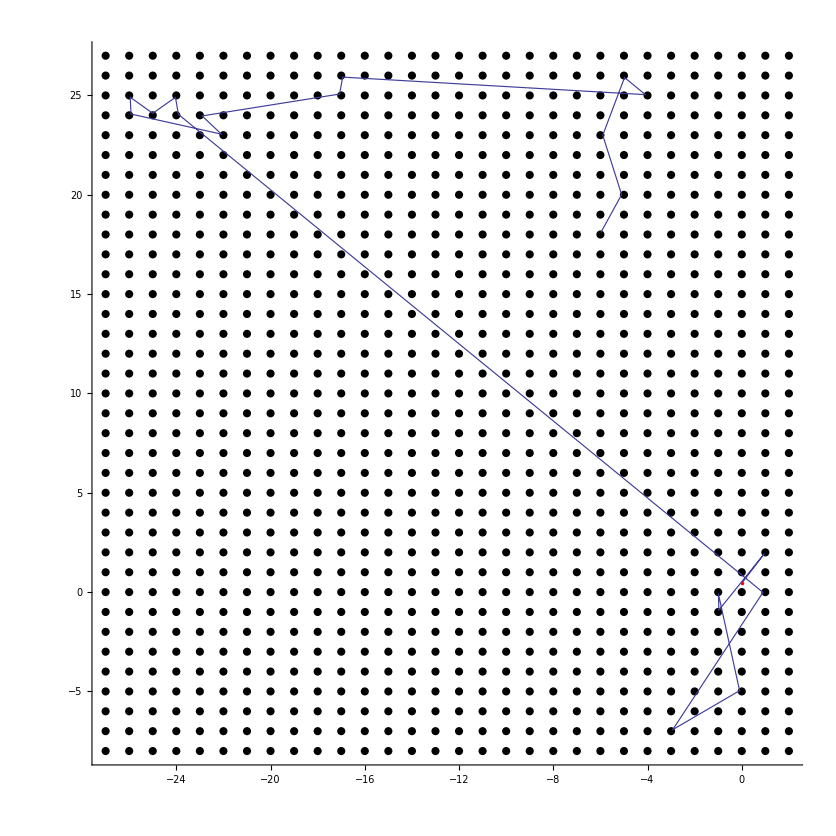

```mathematica
Show[ListPlot[Table[{n,m},{n,-27,2},{m,-8,27}],PlotStyle->Directive[PointSize->0.007,Black],AspectRatio->1],ListPlot[points,Joined->True,PlotStyle->Directive[Thickness[0.001]]],ListPlot[{{0,0.445}},PlotStyle->Directive[PointSize->0.003,Red]]]
```

```mathematica
circles:=ContourPlot[Evaluate[Flatten[Table[(x-n)^2+(y-m)^2==ρ^2,{n,-2,2},{m,-2,2}]]],{x,-2,2},{y,-2,2},Axes->True,AspectRatio->Automatic,ContourStyle->Black,PlotRange->{{-2,2},{-2,2}}]
```

```mathematica
x0:={0, 0.445}
```

```mathematica
v0:={0.215, 0.336}
```

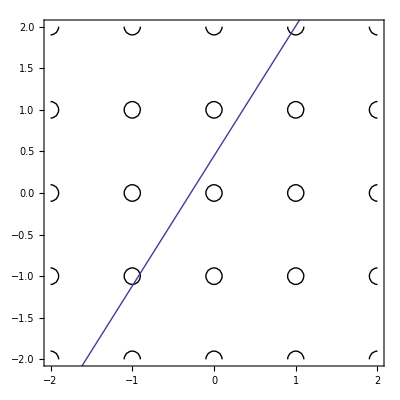

```mathematica
Show[circles,Plot[v0[[2]]/v0[[1]] x+x0[[2]],{x,-2,2}]]
```

```mathematica
(*********************************************************)
```

```mathematica
(* 3D version *)
```

```mathematica
sphere[r_,n_,m_,l_]:=Plot3D[{√(r^2-((x-n)^2+(y-m)^2))+l,-√(r^2-((x-n)^2+(y-m)^2))+l},{x,n-1,n+1},{y,m-1,m+1},BoxRatios->Automatic,AxesLabel->{"x", "y"}]
```

```mathematica
spheres[r_,xmin_,xmax_,ymin_,ymax_,zmin_,zmax_]:=Show[Table[sphere[r,n,m,l],{n,xmin,xmax},{m,ymin,ymax},{l,zmin,zmax}],PlotRange->All]
```

```mathematica
x0 := {0.5,0.5,0.5}
```

```mathematica
v0:={0.1112,0.19779,0.0669}
```

```mathematica
line[x0_,v0_,tmin_,tmax_]:=ParametricPlot3D[{x=x0[[1]]+v0[[1]]t,y=x0[[2]]+v0[[2]]t,z=x0[[3]]+v0[[3]]t},{t,tmin,tmax}]
```

```mathematica
Show[spheres[0.1,0,5,0,5,0,5],line[x0,v0,20]]
```

-Graphics3D-

```mathematica
x0:={0,0.445,0.342}
```

```mathematica
v0:={0.451207,0.541449,0.709398}
```

```mathematica
Show[spheres[0.1,2,4,3,5,4,6],line[x0,v0,4,7]]
```

-Graphics3D-

```mathematica
(* This line intersects the ball (3,4,5), but not through the center *)
```

```mathematica
v1:={-0.4512069325775071,-0.5414489190929208,-0.7093978939968069}
```

```mathematica
x1:={2.92769084745365,3.9582329100898943,4.944982736974214}
```

```mathematica
Show[spheres[0.1,-6,-1,-6,-1,-6,-1],line[x1,v1,8,16]]
```

-Graphics3D-